#### a) Plot the trajectories and classify the fixed points, for the dynamical system for different values of sigma

```mathematica
dotx[x_,y_,sigma_]:= (sigma + 3) * x + 4* y;
doty[x_,y_,sigma_]:= -(9/4) * x + (sigma - 3) * y;
sol1 =  Solve[dotx[x,y,-1] == 0 && doty[x,y,-1]==0,{x,y}]
sol2 =  Solve[dotx[x,y,0] == 0 && doty[x,y,0]==0,{x,y}]
sol3 =  Solve[dotx[x,y,1] == 0 && doty[x,y,1]==0,{x,y}]
(*here is the solutions for the fixed points for the different sigma values*)
```

{{x→0,y→0}}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→-(3 x)/4}}

{{x→0,y→0}}

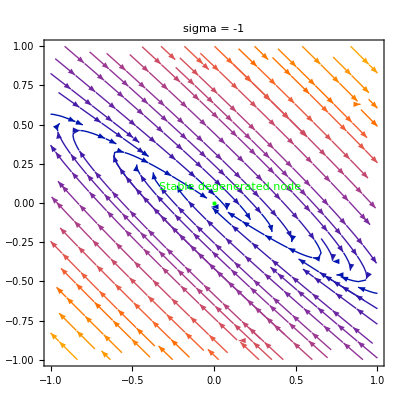

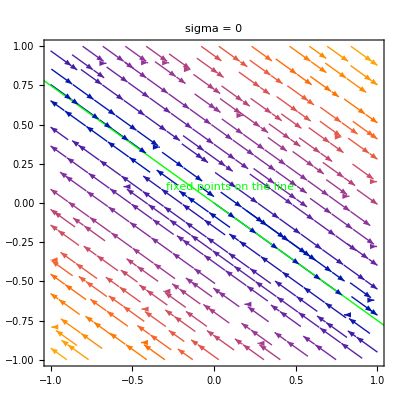

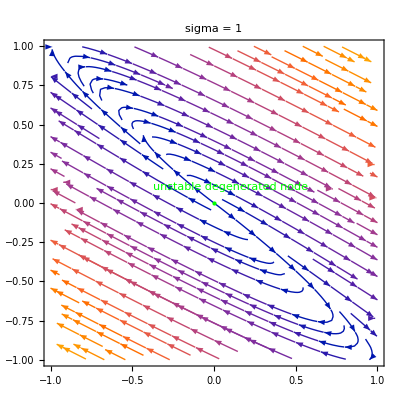

```mathematica
plot1 = StreamPlot[{dotx[x,y,-1],doty[x,y,-1]},{x,-1,1},{y,-1,1},Epilog->{Green,Point[{0,0}],Text["Stable degenerated node",{0.1,0.1}]},PlotLabel->"sigma = -1"];

plot2 = StreamPlot[{dotx[x,y,0],doty[x,y,0]},{x,-1,1},{y,-1,1},Epilog->{Green,Line[{{16/3,-4},{-16/3, 4}}],Text["fixed points on the line",{0.1,0.1}]},PlotLabel->"sigma = 0"]; 

plot3 =  StreamPlot[{dotx[x,y,1],doty[x,y,1]},{x,-1,1},{y,-1,1},Epilog->{Green,Point[{0,0}],Text["unstable degenerated node",{0.1,0.1}]},PlotLabel->"sigma = 1"];

Show[plot1]
Show[plot2]
Show[plot3]
```

### b) Analytically compute eigenvalues of M_sigma in terms of sigma

```mathematica
Clear[sigma];
M= {{sigma + 3, 4}, {-9/4, sigma -3}};
Eigenvalues[M]
```

{sigma,sigma}

#### c) Compute all the eigenvectors of M_q, normalize to one and choose the x-components

```mathematica
eigenvector = Eigenvectors[M];
eigenvector = eigenvector[[1]];
v = Normalize[eigenvector];
v = v*-1
```

{4/5,-3/5}

#### d) Compute the inverse matrix of M_q

```mathematica
inverseM = Inverse[M]
```

{{(-3+sigma)/sigma^2,-4/sigma^2},{9/(4 sigma^2),(3+sigma)/sigma^2}}

#### e) Give the value of sigma for which M_q is singular

M_q is singular when the inverse of M_q does not exist. Form d) we have the inverse of M_q and we can see that it not exist for sigma = 0, which is the answer.

#### f) For which values of c and d do you recover the dynamical system in the excercise above? choose c positive and write the result as the vector [c,d]

```mathematica
Solve[-c*d == 3 && d^2 == 4 && -c^2 == -9/4 && c*d == -3,{c,d}]
```

{{c→-3/2,d→2},{c→3/2,d→-2}}

Choose the one with the positive c

#### g) Calculate the eigenvalues of the generalised dynamical system

```mathematica
M = {{sigma -c*d, d^2}, {-c^2, sigma +c*d}};
Eigenvalues[M]
```

{sigma,sigma}

### h) Analytically find the direction of the line of fixed points for sigma = 0

```mathematica
sigma = 0;
Amatrix = {{sigma-c*d,d^2},{-c^2,sigma + c*d}};
eigenvector= Eigenvectors[Amatrix];
vector = eigenvector[[1]];
vector = Normalize[vector]
```

{d/(c √(1+Abs[d/c]^2)),1/(√(1+Abs[d/c]^2))}